```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichiro/Documents/Univ/SLattice/peak_theory

```mathematica
mapdata=Import["data/mono_map_0.dat"];
```

```mathematica
NL=Length[mapdata[[1]]]^(1/3)
```

256

```mathematica
map3D=Table[mapdata[[1,NL^2(nx-1)+NL(ny-1)+nz]],{nx,NL},{ny,NL},{nz,NL}];
```

```mathematica
powerdata=Import["data/mono_power_0.dat"][[1]];
```

```mathematica
powerList=Table[{i-1,powerdata[[i]]},{i,Length[powerdata]}];
```

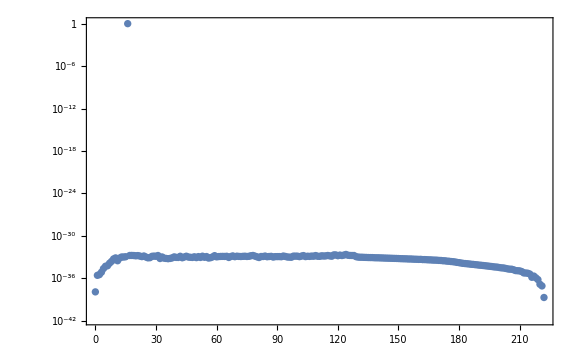

```mathematica
ListLogPlot[powerList,Joined->False]
```